```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Defect_annealed/DOS"];
file={"DOS_all"};
dosAll=ReadList[file[[1]],{Number, Number}];
labeldos={"4575","4.625","4.6583","4.685","4.6910 (Exp.)","4730","4759","4801","4850"}
```

{4575,4.625,4.6583,4.685,4.6910 (Exp.),4730,4759,4801,4850}

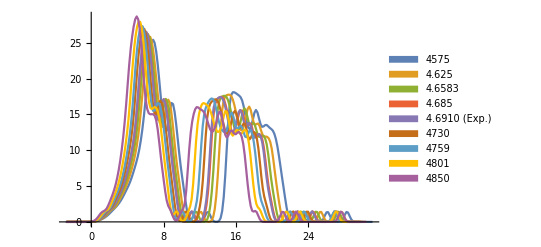

```mathematica
ListPlot[Table[Partition[dosAll,201][[i]],{i,1,9}],PlotLegends->SwatchLegend[labeldos],Joined->True]
```

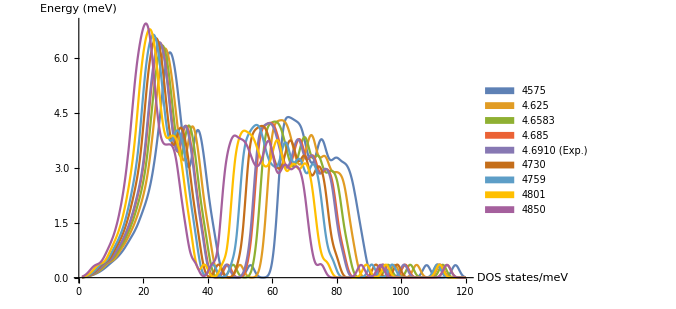

```mathematica
DOSfits=Table[Interpolation[Partition[dosAll,201][[i]]],{i,1,9}];
Plot[Evaluate@Table[(1/4.135665538536)*DOSfits[[i]][x/4.135665538536],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
qhaDefect={"QHA_defect/e-v.dat","QHA_defect/volume_expansion.dat","QHA_defect/volume-temperature.dat","QHA_defect/gruneisen-temperature.dat","QHA_defect/gibbs-temperature.dat","QHA_defect/bulk_modulus-temperature.dat","QHA_defect/Cp-temperature.dat","QHA_defect/dsdv-temperature.dat"};
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
swatch=PlotLegends->SwatchLegend[{"Defective","Perfect"}];
defect=Table[ReadList[qhaDefect[[i]],{Number, Number}],{i,1,8}];
normal=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,1,8}];
```

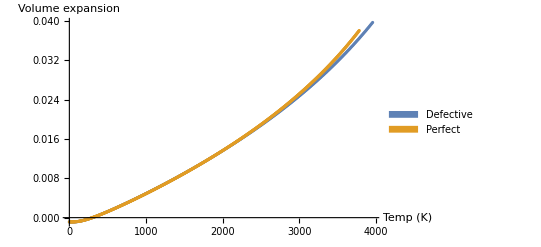

```mathematica
(*Volume expansion*)
ListPlot[{defect[[2]],normal[[2]]},swatch,AxesLabel->{"Temp\n(K)","Volume\n expansion"}]
```

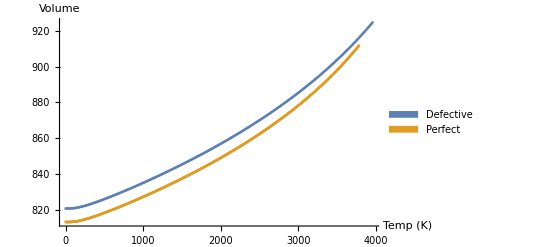

```mathematica
(*Volume-Temperature*)
ListPlot[{defect[[3]],normal[[3]]},swatch,AxesLabel->{"Temp\n(K)","Volume"}]
```

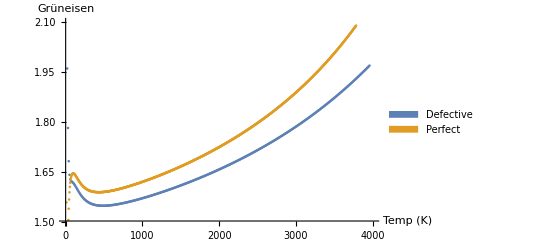

```mathematica
(*Gruneisen-Temperature*)
ListPlot[{defect[[4]],normal[[4]]},PlotRange->{{0,4000},{1.5,2.1}},swatch,AxesLabel->{"Temp\n(K)","Grüneisen"}]
```

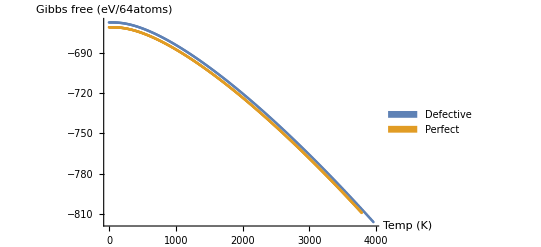

```mathematica
(*Gibbs-Temperature*)
ListPlot[{defect[[5]],normal[[5]]},swatch,AxesLabel->{"Temp\n(K)","Gibbs free\n(eV/64atoms)"},PlotRange->{{0,4000},{-660,-820}}]
```

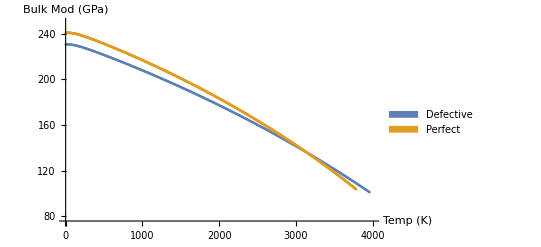

```mathematica
(*Bulkmod-Temperature*)
ListPlot[{defect[[6]],normal[[6]]},swatch,PlotRange->{{0,4000},{75,250}},AxesLabel->{"Temp\n(K)","Bulk Mod\n(GPa)"}]
```

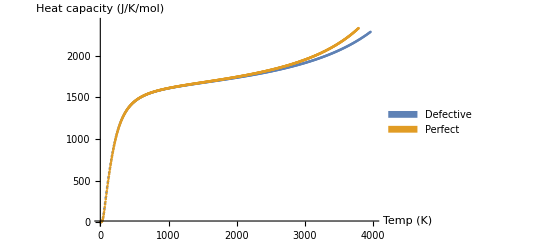

```mathematica
(*Cp-Temperature*)
ListPlot[{defect[[7]],normal[[7]]},PlotRange->{{0,4000},{1,2400}},swatch,AxesLabel->{"Temp\n(K)","Heat capacity\n(J/K/mol)"}]
```

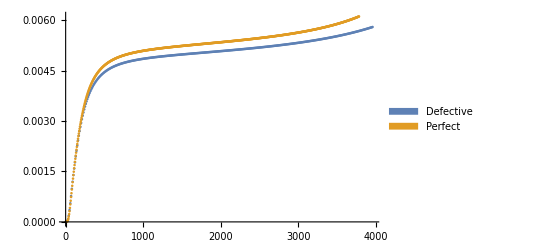

```mathematica
(*dSdV-Temperature*)
ListPlot[{defect[[8]],normal[[8]]},swatch]
```